#### Goebner basis. Example 1.

## Basic Examples

A section to get a feel for grobner basis. In order to do this we shall look at an example.

### Example 1.

Consider the system of polynomials
	, and 
In which we want to find the points of intersection, namely when .
Lets plot this system.

```mathematica
f[x_,y_]:= x^2-y^2
g[x_, y_]:= x^3-y^2-1
```

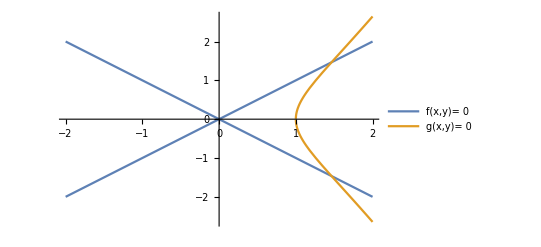

```mathematica
ex1Plot = Plot[{y/. Solve[f[x,y]==0],y/. Solve[g[x,y]==0]}, { x, -2,2}, PlotLegends->{"f(x,y)= 0","g(x,y)= 0"}]
```

Here we note that there must exist two solutions to the intersection of both these curves. One method that we already know to find these is to use the solver such as ( Only looking at solutions in the reals):

```mathematica
Solve[ f[x,y]==0 && g[x,y]==0,{x,y},Reals]
```

{{x→Root1.47Root[-1-#1^2+#1^3&,1]1.465571231876768,y→-Root1.47Root[-1-#1^2+#1^3&,1]1.465571231876768},{x→Root1.47Root[-1-#1^2+#1^3&,1]1.465571231876768,y→Root1.47Root[-1-#1^2+#1^3&,1]1.465571231876768}}

Alternatively we can apply Groben Basis, (create our own alg):

```mathematica
ex1grob = GroebnerBasis[{f[x,y],g[x,y]},{x,y}]
```

{-1-2 y^2-y^4+y^6,1+x+y^2-y^4}

Here, note that we have two polynomials, however one is only dependent on the variable  . In essence simplifying  the systems so it becomes easier to analysis. We claim that the points of intersection of  are the same as  (here prime notation does not represent the derivative) , this we many see if we plot the new system.

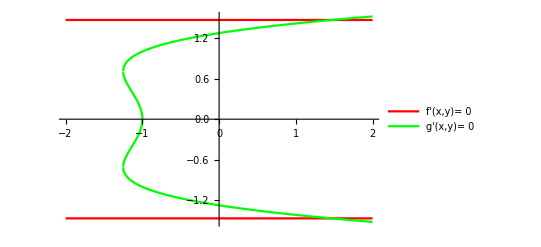

```mathematica
ex1Plot2= Plot[{y/. Solve[ex1grob[[1]]==0],y/. Solve[ex1grob[[2]]==0]}, { x, -2,2}, PlotLegends->{"f'(x,y)= 0","g'(x,y)= 0"}, PlotStyle->{Red,Green}]
```

Now side-by-side

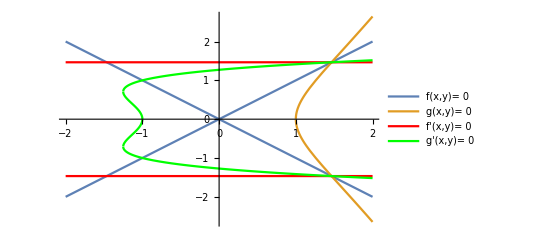

```mathematica
ex1Plot3 = Show[ex1Plot,ex1Plot2]
```

Now by the solver

```mathematica
Solve[ex1grob[[1]]==0 && ex1grob[[2]]==0, {x,y}, Reals]
```

{{x→Root1.47Root[{-1-#1^2+#1^3&,-#1+#2&},{1,1}]1.465571231876768,y→Root1.47Root[-1-#1^2+#1^3&,1]1.465571231876768},{x→Root1.47Root[{1+#1^2+#1^3&,#1+#2&},{1,1}]1.465571231876768,y→Root-1.47Root[1+#1^2+#1^3&,1]-1.465571231876768}}

Which we see are the same points as the original system of polynomials. Hence  these systems are equivalent.

Now we compute the reduce Groeben bases for the other orderings.

```mathematica
For
```

```mathematica
ex1grobRE= GroebnerBasis[{f[x,y],g[x,y]},{x,y}, MonomialOrder->DegreeReverseLexicographic]
```

{x^2-y^2,-1-y^2+x y^2,-1-x-y^2+y^4}

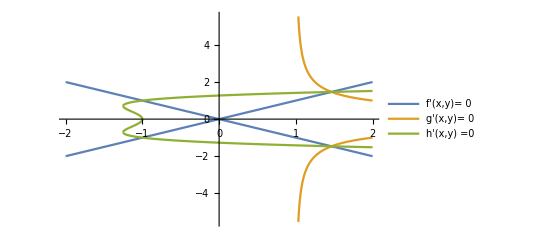

```mathematica
ex1Plot3= Plot[{y/. Solve[ex1grobRE[[1]]==0],y/. Solve[ex1grobRE[[2]]==0],y/. Solve[ex1grobRE[[3]]==0]}, { x, -2,2}, PlotLegends->{"f'(x,y)= 0","g'(x,y)= 0","h'(x,y) =0"}]
```

```mathematica
ex1grobDlex= GroebnerBasis[{f[x,y],g[x,y]},{x,y}, MonomialOrder->DegreeLexicographic]
```

{x^2-y^2,-1-y^2+x y^2,-1-x-y^2+y^4}

```mathematica
Plot[{y/. Solve[ex1grobDlex[[1]]==0],y/. Solve[ex1grobDlex[[2]]==0],y/. Solve[ex1grobDlex[[3]]==0]}, { x, -2,2}, PlotLegends->{"f'(x,y)= 0","g'(x,y)= 0","h'(x,y) =0"}]
```

-Graphics-